```mathematica
rawdata=Import[NotebookDirectory[]~~"MonteCarloRun1.csv"]
```

```mathematica
data=Rest[rawdata]
```

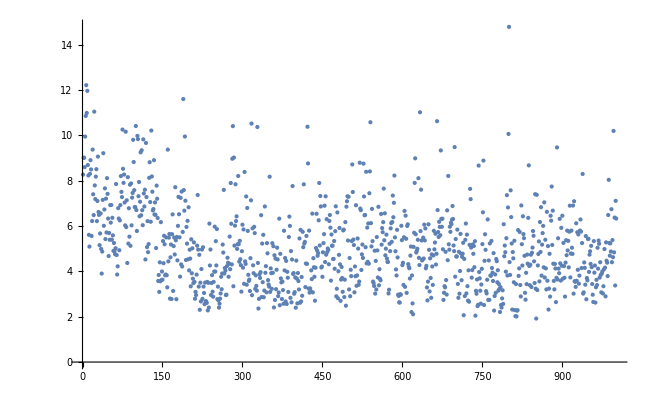

```mathematica
chisqs=data[[;;;;100,12]];
ListPlot[chisqs]
```

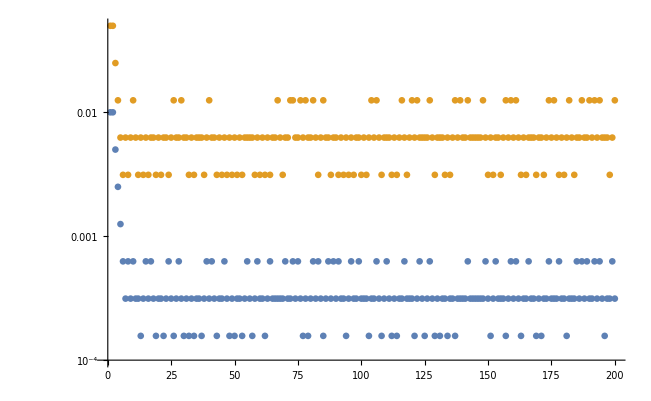

```mathematica
stepsizes=data[[All,13;;14]];
ListLogPlot[Transpose[stepsizes][[All,1;;UpTo[20000];;100]]]
```

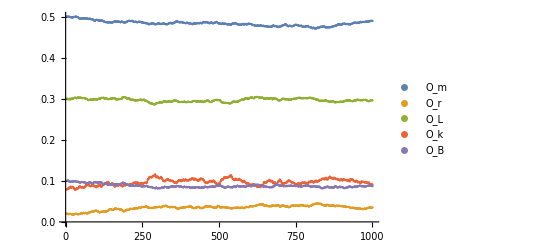

```mathematica
cosmoparams=Transpose[data[[;;;;100,2;;6]]];
ListPlot[cosmoparams,PlotLegends->rawdata[[1,2;;6]]]
```

```mathematica
nvectors=data[[All,9;;11]]
ListPointPlot3D[{nvectors[[;;;;100]],{Last[nvectors]}}]
```

-Graphics3D-

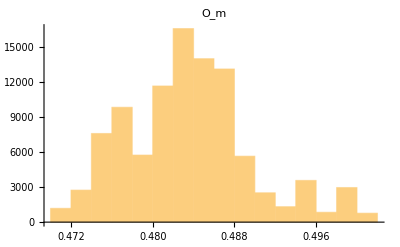
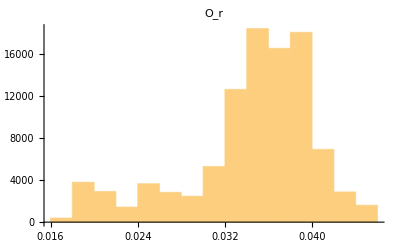
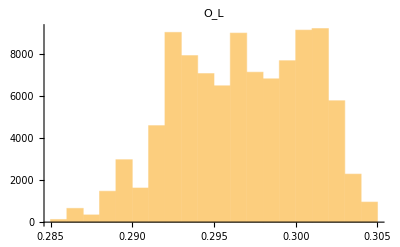
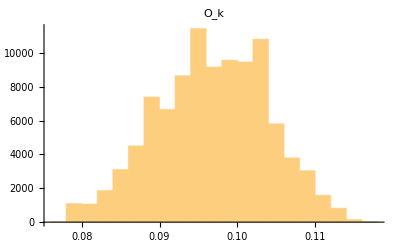
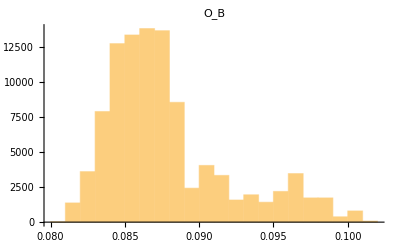
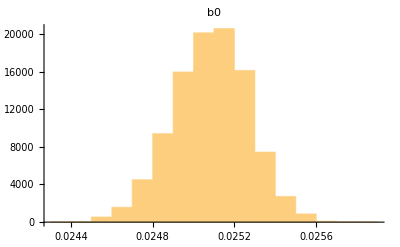
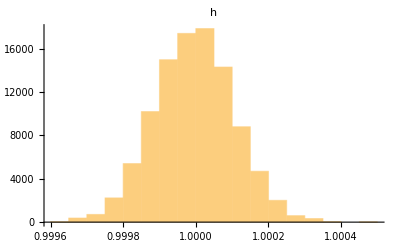

```mathematica
Table[Histogram[data[[All,i]],PlotLabel->rawdata[[1,i]]],{i,2,8}]
```